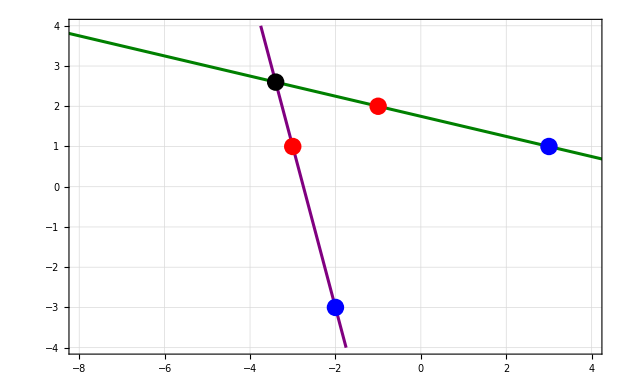

```mathematica
x4=Plot [1.75 - x/4,{x,-10,6},PlotStyle->{RGBColor["Green"],Thickness[0.0035]},FrameStyle->Directive[Black,20],Frame->True,FrameLabel->{Style["",30,Black,FontFamily->"Cambria"],Style["",30,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{-8,4},{-4,4}}];
x5=Plot [-11 - 4x,{x,-10,6},PlotStyle->{RGBColor["Purple"],Thickness[0.0035]},FrameStyle->Directive[Black,20],Frame->True,FrameLabel->{Style["",30,Black,FontFamily->"Cambria"],Style["",30,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{-8,4},{-4,4}}];
i1=Graphics[{PointSize[0.02],RGBColor["Red"],Point[{-1,2}]}];
i2=Graphics[{PointSize[0.02],RGBColor["Blue"],Point[{3,1}]}];
i3=Graphics[{PointSize[0.02],RGBColor["Red"],Point[{-3,1}]}];
i4=Graphics[{PointSize[0.02],RGBColor["Blue"],Point[{-2,-3}]}];
i5=Graphics[{PointSize[0.02],RGBColor["Black"],Point[{-3.4,2.6}]}];
Show[x4, x5,i1,i2,i3,i4,i5]
```

```mathematica
i1=Graphics[{PointSize[0.02],RGBColor["Black"],Point[{-1,2}]}];
```

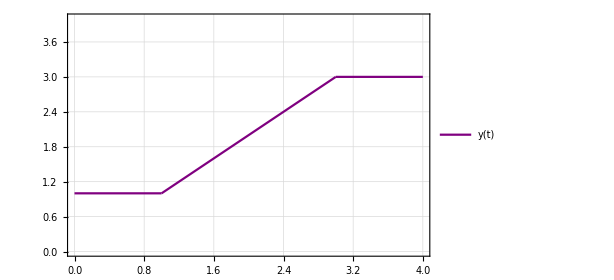

```mathematica
y1=Plot [1,{x,0,1},PlotStyle->{RGBColor["Purple"],Thickness[0.0035]},FrameStyle->Directive[Black,20],Frame->True,FrameLabel->{Style["",30,Black,FontFamily->"Cambria"],Style["",30,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,4},{0,4}},PlotLegends->Placed[LineLegend[{RGBColor["Purple"]},{Style["y(t)",20,Black,FontFamily->"Cambria"]}],{0.1,0.8}]];
y2=Plot [1+x-1,{x,1,3},PlotStyle->{RGBColor["Purple"],Thickness[0.0035]},FrameStyle->Directive[Black,20],Frame->True,FrameLabel->{Style["",30,Black,FontFamily->"Cambria"],Style["",30,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,4},{0,3}}];
y3=Plot [3,{x,3,4},PlotStyle->{RGBColor["Purple"],Thickness[0.0035]},FrameStyle->Directive[Black,20],Frame->True,FrameLabel->{Style["",30,Black,FontFamily->"Cambria"],Style["",30,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,4},{0,3}}];

Show[y1,y2,y3]
```